## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.3; Q=0.99;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.183949+2.69646×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.260283

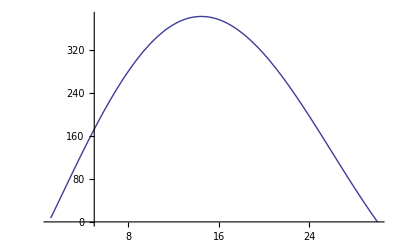

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,2.69649×10^-8},{30.2,2.65483×10^-8},{30.4,2.61365×10^-8},{30.6,2.57281×10^-8},{30.8,2.53252×10^-8},{31.,2.49266×10^-8},{31.2,2.45337×10^-8},{31.4,2.41442×10^-8},{31.6,2.37622×10^-8},{31.8,2.3383×10^-8},{32.,2.30107×10^-8},{32.2,2.26428×10^-8},{32.4,2.22794×10^-8},{32.6,2.19213×10^-8},{32.8,2.15684×10^-8},{33.,2.12204×10^-8},{33.2,2.08774×10^-8},{33.4,2.05397×10^-8},{33.6,2.02064×10^-8},{33.8,1.98781×10^-8},{34.,1.95553×10^-8},{34.2,1.92324×10^-8},{34.4,1.89238×10^-8},{34.6,1.86153×10^-8},{34.8,1.83114×10^-8},{35.,1.80116×10^-8},{35.2,1.77158×10^-8},{35.4,1.74285×10^-8},{35.6,1.71403×10^-8},{35.8,1.68633×10^-8},{36.,1.6587×10^-8},{36.2,1.63154×10^-8},{36.4,1.6048×10^-8},{36.6,1.57973×10^-8},{36.8,1.55269×10^-8},{37.,1.52725×10^-8},{37.2,1.50224×10^-8},{37.4,1.47761×10^-8},{37.6,1.45342×10^-8},{37.8,1.43364×10^-8},{38.,1.40623×10^-8},{38.2,1.38322×10^-8},{38.4,1.36059×10^-8},{38.6,1.33787×10^-8},{38.8,1.31553×10^-8},{39.,1.29502×10^-8},{39.2,1.27382×10^-8},{39.4,1.25305×10^-8},{39.6,1.23262×10^-8},{39.8,1.20749×10^-8},{40.,1.19273×10^-8},{40.2,1.17331×10^-8},{40.4,1.15423×10^-8},{40.6,1.13515×10^-8},{40.8,1.11584×10^-8},{41.,1.09887×10^-8},{41.2,1.08106×10^-8},{41.4,1.06354×10^-8},{41.6,1.04632×10^-8},{41.8,1.0294×10^-8},{42.,1.01276×10^-8},{42.2,9.96433×10^-9},{42.4,9.80436×10^-9},{42.6,9.64539×10^-9},{42.8,9.4834×10^-9},{43.,9.33763×10^-9},{43.2,9.18753×10^-9},{43.4,9.03969×10^-9},{43.6,8.89526×10^-9},{43.8,8.75286×10^-9},{44.,8.61305×10^-9},{44.2,8.47529×10^-9},{44.4,8.34007×10^-9},{44.6,8.20717×10^-9},{44.8,8.07679×10^-9},{45.,7.94832×10^-9},{45.2,7.82195×10^-9},{45.4,7.69799×10^-9},{45.6,7.57598×10^-9},{45.8,7.4561×10^-9},{46.,7.33844×10^-9},{46.2,7.22206×10^-9},{46.4,7.10877×10^-9},{46.6,6.9972×10^-9},{46.8,6.88698×10^-9},{47.,6.77892×10^-9},{47.2,6.6695×10^-9},{47.4,6.56818×10^-9},{47.6,6.4656×10^-9},{47.8,6.36727×10^-9},{48.,6.26552×10^-9},{48.2,6.16798×10^-9},{48.4,6.07213×10^-9},{48.6,5.97801×10^-9},{48.8,5.88523×10^-9},{49.,5.79418×10^-9},{49.2,5.70398×10^-9},{49.4,5.61668×10^-9},{49.6,5.53033×10^-9},{49.8,5.4449×10^-9},{50.,5.36142×10^-9},{50.2,5.27918×10^-9},{50.4,5.19842×10^-9},{50.6,5.11885×10^-9},{50.8,5.04082×10^-9},{51.,4.96389×10^-9},{51.2,4.88842×10^-9},{51.4,4.81406×10^-9},{51.6,4.74101×10^-9},{51.8,4.66918×10^-9},{52.,4.5987×10^-9},{52.2,4.52908×10^-9},{52.4,4.46079×10^-9},{52.6,4.39407×10^-9},{52.8,4.32768×10^-9},{53.,4.26148×10^-9},{53.2,4.19889×10^-9},{53.4,4.13593×10^-9},{53.6,4.07413×10^-9},{53.8,4.01355×10^-9},{54.,3.95363×10^-9},{54.2,3.89496×10^-9},{54.4,3.83702×10^-9},{54.6,3.78018×10^-9},{54.8,3.7243×10^-9},{55.,3.66934×10^-9},{55.2,3.61512×10^-9},{55.4,3.56194×10^-9},{55.6,3.50953×10^-9},{55.8,3.4581×10^-9},{56.,3.40747×10^-9},{56.2,3.35751×10^-9},{56.4,3.30854×10^-9},{56.6,3.26027×10^-9},{56.8,3.21278×10^-9},{57.,3.16422×10^-9},{57.2,3.12021×10^-9},{57.4,3.07707×10^-9},{57.6,3.03054×10^-9},{57.8,2.98682×10^-9},{58.,2.94371×10^-9},{58.2,2.90141×10^-9},{58.4,2.85968×10^-9},{58.6,2.81873×10^-9},{58.8,2.77838×10^-9},{59.,2.73864×10^-9},{59.2,2.69956×10^-9},{59.4,2.66101×10^-9},{59.6,2.62319×10^-9},{59.8,2.58595×10^-9},{60.,2.54935×10^-9},{60.2,2.51326×10^-9},{60.4,2.47761×10^-9},{60.6,2.44274×10^-9},{60.8,2.40838×10^-9},{61.,2.37447×10^-9},{61.2,2.3412×10^-9},{61.4,2.30833×10^-9},{61.6,2.27605×10^-9},{61.8,2.24425×10^-9},{62.,2.21302×10^-9},{62.2,2.1822×10^-9},{62.4,2.15119×10^-9},{62.6,2.11465×10^-9},{62.8,2.0926×10^-9},{63.,2.06473×10^-9},{63.2,2.03517×10^-9},{63.4,2.00716×10^-9},{63.6,1.97957×10^-9},{63.8,1.96643×10^-9},{64.,1.92562×10^-9},{64.2,1.89924×10^-9},{64.4,1.87573×10^-9},{64.6,1.84773×10^-9},{64.8,1.82253×10^-9},{65.,1.79778×10^-9},{65.2,1.77338×10^-9},{65.4,1.74933×10^-9},{65.6,1.71886×10^-9},{65.8,1.70236×10^-9},{66.,1.6794×10^-9},{66.2,1.65677×10^-9},{66.4,1.63452×10^-9},{66.6,1.61259×10^-9},{66.8,1.591×10^-9},{67.,1.56971×10^-9},{67.2,1.54875×10^-9},{67.4,1.52811×10^-9},{67.6,1.50778×10^-9},{67.8,1.48775×10^-9},{68.,1.46802×10^-9},{68.2,1.44858×10^-9},{68.4,1.42946×10^-9},{68.6,1.41057×10^-9},{68.8,1.39198×10^-9},{69.,1.37366×10^-9},{69.2,1.35563×10^-9},{69.4,1.33786×10^-9},{69.6,1.32032×10^-9},{69.8,1.3031×10^-9},{70.,1.2863×10^-9}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

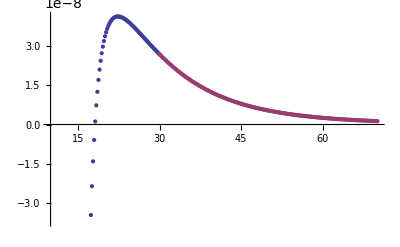

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

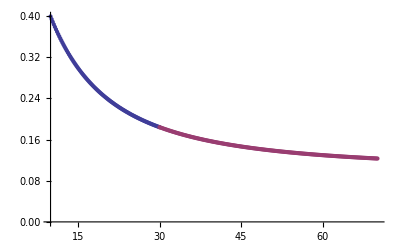

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.3/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.3/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.3/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.3/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```